```mathematica
SetDirectory[FileNameJoin[{ParentDirectory@NotebookDirectory[], "data"}]]
```

/Users/arsenytokarev/Desktop/CourseWorks/Gas Dynamics/Code/data

```mathematica
NormalRepresentation[data_List]:= Module[
{solution, mesh},
solution = {ToExpression@#⟦1⟧, #⟦2⟧} &/@ data;
For[i =1, i <= Length@solution, ++i,
 solution⟦i,2⟧ = {ToExpression@#⟦1⟧, ToExpression@#⟦2⟧} &/@ solution⟦i,2⟧
];
Return@solution
];
```

```mathematica
advection = NormalRepresentation@Import["advection.json"] ;
```

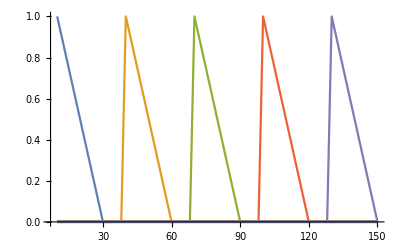

```mathematica
ListLinePlot[Take[(#⟦2⟧ &/@ advection), {1, -1, 15}], PlotRange->All]
```